## Comparison to numerical solution

### Calling functions

```mathematica
(* Set up linkage with the cell engine *)
Dynamic[{linked`Kn,linked`Kt,linked`Kl,linked`Dp,linked`Dl,
linked`phiParB,linked`phiParL,linked`phiParR,linked`threshDivide,
linked`initialCond,linked`nbCyc,linked`excludeNb,linked`flag}];
Dynamic[{dataGrowthRate,dataMolecularSpecies}];
Dynamic[return];
```

```mathematica
(* Calling function *)
callCellEngine[kn_,kt_,kl_,dp_,dl_,
phiB_,phiL_,phiR_,xDiv_,
initialCond_,cycCount_,excludeCyc_,flag_]:=Module[{},

linked`Kn=kn;
linked`Kt=kt;
linked`Kl=kl;

linked`Dp=dp;
linked`Dl=dl;

linked`phiParB=phiB;
linked`phiParL=phiL;
linked`phiParR=phiR;
linked`threshDivide=xDiv;

linked`nbCyc=cycCount;
linked`flag=flag;
linked`initialCond=initialCond;
linked`$callingNotebook=EvaluationNotebook[];
return=NotebookEvaluate["/home/bogi/Desktop/growth_rate/notebooks/numerical/cellEngine_0513.nb"];
];
```

### Comparison of steady-state analytical solution with numerically integrated ODEs

```mathematica
return=. (* clear return var *);
```

```mathematica
κlPar=50;
κtPar=1;
κnPar=10;
dpPar=0.1;
dlPar=0.1;

phiB=0.5;
phiL=0.1;
phiR=0.4;

xDiv=10^9;

cycCount=20;
excludeCyc=10;
flag="deterministic";
initialCond1={10*10^5,10*10^5,10^5,2*10^5,2*10^5};
initialCond2={5*10^5,5*10^5,10^5,10^5,10^5};
initialCond3={10*10^5,10*10^5,10^5,2*10^5,10^5};
initialCond4={5*10^5,5*10^5,10^5,2*10^5,2*10^5};
initialCond5={10*10^5,10*10^5,10^5,2*10^5,2*10^5};
```

```mathematica
callCellEngine[κnPar,κtPar,κlPar,dpPar,dlPar,phiB,phiL,phiR,xDiv,initialCond5,cycCount,excludeCyc,flag]
```

```mathematica
(* assign returned values to vars for plotting *)
tArray=return[[1]];
retStateVars=return[[2]];
sol=return[[3]];
```

```mathematica
(* split the time-series *)
varPlotRange=cycCount;
timeSeriesB=MapIndexed[retStateVars[[#1]][[1]]&,Table[i,{i,1,varPlotRange}]];
timeSeriesL=MapIndexed[retStateVars[[#1]][[2]]&,Table[i,{i,1,varPlotRange}]];
timeSeriesR=MapIndexed[retStateVars[[#1]][[3]]&,Table[i,{i,1,varPlotRange}]];
timeSeriesPb=MapIndexed[retStateVars[[#1]][[4]]&,Table[i,{i,1,varPlotRange}]];
timeSeriesPl=MapIndexed[retStateVars[[#1]][[5]]&,Table[i,{i,1,varPlotRange}]];
```

```mathematica
timeSeriesTime=Part[tArray,1;;varPlotRange];
```

```mathematica
(* B, L, R, Pb, Pl *)
```

```mathematica
ssLambda=1/(2 ((1+Km) κl ϕl+κt ϕr))κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr))));
```

```mathematica
Clear[V]
```

```mathematica
abundanceVector=({{(Km κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))) V[t])/(2 ((1+Km) κl ϕl+κt ϕr) (κt ϕr-(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))))}, {(Km κl κt^3 ϕl ϕr^3 (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr))))^3 V[t])/(8 ls ((1+Km) κl ϕl+κt ϕr)^3 (dl+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))) (-κt ϕr+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))) ((κl κt ϕl ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))+κt ϕr (dp-κn ϕb+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr)))))}, {(Km κt^2 ϕr^3 (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))) (dp+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))) V[t])/(2 lr ((1+Km) κl ϕl+κt ϕr) (-κt ϕr+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))) ((κl κt ϕl ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))+κt ϕr (dp-κn ϕb+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr)))))}, {(Km κt^3 ϕb ϕr^3 (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr))))^2 V[t])/(4 lp ((1+Km) κl ϕl+κt ϕr)^2 (-κt ϕr+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))) ((κl κt ϕl ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))+κt ϕr (dp-κn ϕb+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr)))))}, {(Km κt^3 ϕl ϕr^3 (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr))))^2 V[t])/(4 lp ((1+Km) κl ϕl+κt ϕr)^2 (-κt ϕr+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))) ((κl κt ϕl ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr))+κt ϕr (dp-κn ϕb+(κt ϕr (-dp-dp Km ϕb+κn ϕb+Km κn ϕb-dp Km ϕl+κl ϕl+κt ϕr-√(((1+Km) κn ϕb+κl ϕl+dp (-1+Km (-1+ϕr))+κt ϕr)^2+4 ((1+Km) κl ϕl+κt ϕr) (dp+κn (-1+ϕl+ϕr)))))/(2 ((1+Km) κl ϕl+κt ϕr)))))}})/.V[t]->xDiv;
```

```mathematica
analyticSol=Plot[ssLambda,{x,1,varPlotRange},PlotTheme->"Monochrome",
Frame->True,FrameLabel->{"Cell division event","Growth rate (h^-1)"},PlotRange->{0.2,0.7},FrameStyle->Directive[Black,FontSize->15],PlotStyle->{Red,Thickness[0.005]},ImageSize->Large];
plotLambda5=ListLinePlot[{
Log[2]/timeSeriesTime
},PlotTheme->"Monochrome",PlotMarkers->{"▼", "○", "□", "◇"},
Frame->True,FrameLabel->{"Cell division event","Growth rate, λ (h^-1)"},PlotRange->{0.2,0.7},FrameStyle->Directive[Black,FontSize->20,Thickness[0.005]],LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold},ImageSize->Large,AspectRatio->1];
```

# Molecular abundances in the steady state

```mathematica
g1=Show[plotLambda5,plotLambda1,plotLambda2,plotLambda3,plotLambda4,analyticSol,ImageSize->Medium,
Epilog->Inset[Column[{PointLegend[{Black},{"    Numerical integration"}],LineLegend[{Red},{"Steady-state analytics"}]}],Scaled[{0.7,0.85}]]];
```

```mathematica
(* Function returns sol based on time t *)
timeCond[t_]:=Flatten[
Position[
Map[
If[#==1,0≤t<tArray[[#]],
Sum[tArray[[j]],{j,1,#-1}]≤t<Sum[tArray[[j]],{j,1,#}]]&,
Table[i,{i,1,varPlotRange}]],
True]
][[1]]
```

```mathematica
(* B, L, R, Pb, Pl *)
```

```mathematica
g2=Plot[{
B[t]/.sol[[timeCond[x]]]/.{t->x-Sum[tArray[[i]],{i,1,timeCond[x]-1}]},abundanceVector[[1]],
L[t]/.sol[[timeCond[x]]]/.{t->x-Sum[tArray[[i]],{i,1,timeCond[x]-1}]},abundanceVector[[2]],
R[t]/.sol[[timeCond[x]]]/.{t->x-Sum[tArray[[i]],{i,1,timeCond[x]-1}]},abundanceVector[[3]],
Pb[t]/.sol[[timeCond[x]]]/.{t->x-Sum[tArray[[i]],{i,1,timeCond[x]-1}]},abundanceVector[[4]],
Pl[t]/.sol[[timeCond[x]]]/.{t->x-Sum[tArray[[i]],{i,1,timeCond[x]-1}]},abundanceVector[[5]]
},
{x,0,Sum[tArray[[i]],{i,1,varPlotRange}]},PlotTheme->"Scientific",AspectRatio->1,PlotLegends->{"B",None,"L",None,"R",None,"P_b",None,"P_l",None},Frame->True,FrameLabel->{"Time (h)","Abundance (molecs)"},PlotRange->All,ScalingFunctions->{None,"Log10"},PlotStyle->{
ColorData[97,1],{ColorData[97,1],Dashed},
ColorData[97,2],{ColorData[97,2],Dashed},
ColorData[97,3],{ColorData[97,3],Dashed},
ColorData[97,4],{ColorData[97,4],Dashed},
ColorData[97,5],{ColorData[97,5],Dashed}
},ImageSize->Medium,FrameStyle->Directive[Black,FontSize->20,Thickness[0.0075]],LabelStyle->{FontSize->15,FontFamily->"Times",Black,Bold}];
```

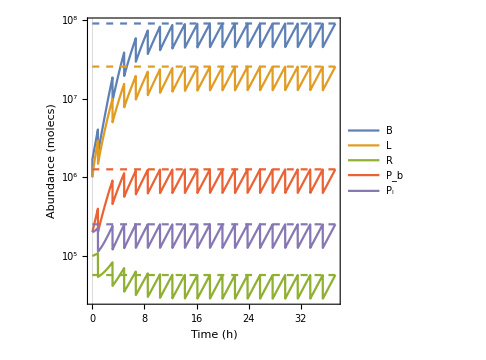
-Graphics- | -Graphics-

```mathematica
Grid[{{g1,g2}}]
```